```mathematica
t=1;
a=1;
sigma1={{0,1},{1,0}};
sigma3={{1,0},{0,-1}};
matH=-(t-t1)Sin[k a]sigma1+(2t1+2(t-t1)(Sin[(k a)/2])^2)sigma3;
eigenH=Eigenvalues[matH];
a=Table[Plot[{eigenH[[1]],eigenH[[2]]},{k,-Pi/a,Pi/a}],{t1,-0.2,0.2,0.01}];
Export["SSHenergy.gif",a]
```

SSHenergy.gif

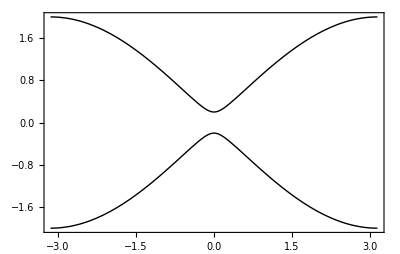

```mathematica
t=1;
a=1;
t1=-0.1;
sigma1={{0,1},{1,0}};
sigma3={{1,0},{0,-1}};
matH=-(t-t1)Sin[k a]sigma1+(2t1+2(t-t1)(Sin[(k a)/2])^2)sigma3;
eigenH=Eigenvalues[matH];
a=Plot[{eigenH[[1]],eigenH[[2]]},{k,-Pi/a,Pi/a},Frame->True,Axes->False,PlotStyle->{Directive[Black,Thick],Directive[Black,Thick]},AspectRatio->Automatic]
```

```mathematica
Export["C:\Users\Fluen\Desktop\李成蹊所有的note\shen-note\SSHenergy3.pdf",a]
```

C:\Users\Fluen\Desktop\李成蹊所有的note\shen-note\SSHenergy3.pdf